# A fast marching solver with adaptive stencils

This Mathematica notebook is intended as a companion notebook for the manuscript : Jean - Marie Mirebeau, Jorg Portegies, "Hamiltonian Fast Marching: A numerical solver for anisotropic and non-holonomic eikonal PDEs", 2018 (submitted) and as documentation for the HamiltonFastMarching (HFM) library, which also has interfaces to the Matlab® and Python languages. For a more extended version of this notebook in Python, see here, and for an overview of other Python notebooks demonstrating the HFM library functionality, see this summary.

In this notebook, we demonstrate anisotropic Riemannian fast marching, in two and three dimensions. The implementation and the numerical examples are based on the paper:

[Mir17] J.-M. Mirebeau, “Anisotropic fast-marching on cartesian grids using Voronoi’s first reduction of quadratic forms,” HAL (Preprint). 2017.
 
More formally, we numerically solve Riemannian eikonal equations, and backtrack the corresponding minimal geodesics. In order to describe this mathematical problem, we need to introduce some notation. Let Ω ⊂ ℝ be a domain, let D:Ω→ S^(++)(ℝ^d) be a field of positive definite tensors, and let σ : ∂Ω → (-∞,∞] denote some boundary data. We seek the viscosity solution u:Ω̄ → (-∞,∞] to the PDE

∀x∈Ω, (‖∇u[x]‖)_D[x]=1, ∀x∈∂Ω, u[x]=σ[x].

We denote by (‖v‖)_D:=√(v^T·D·v) the anisotropic norm of a vector v∈ℝ^d defined by a positive definite tensor D∈S^(++)(ℝ^d).
The solution value u[x] for x∈Ω is known to be the minimal Riemannian length (plus the initial penalization σ) of a path γ:[0,1]→Ω̄  from ∂Ω to x.

u[x]=inf_((γ[0]∈∂Ω)_(γ[1]=x)) σ[γ[0]]+(∫_0)^1(‖γ'[t]‖)_M[γ[t]]dt.

In the last equation, path length is measured using the Riemannian metric M:Ω→ S^(++)(ℝ^d) defined as the inverse M=D^-1 of the tensor fields appearing in the eikonal PDE.

## A. Showcase of the HFM library functionality

III - Riemannian metrics

## Directory settings

In this series of notebooks, input and output to the HamiltonFastMarching library is based on files written on the disk. Change the following directory settings to work on your own machine.

```mathematica
(*directory with fast marching executable*)
(*hfmexeDirectory = "C:\\Users\\jportegi\\stack\\PostDoc\\Fast-Marching\\HamiltonFastMarching-master\\bin\\";(*Windows format*)*)
hfmexeDirectory = "/Users/mirebeau/bin/2018/FileHFM/Release"; (*Linux/MacOs format*)

(*directory where experiments should be placed*)
hfmoutputDirectory=FileNameJoin[{NotebookDirectory[],"experiments"}];
(*In case hfmoutputDirectory does not exist, it needs to be created*)
If[!DirectoryQ[hfmoutputDirectory],CreateDirectory[hfmoutputDirectory]]
```

## Functions to call external Fast Marching solver

```mathematica
(*Function to call the HFM executable with the desired parameters, and import the result to Mathematica*)
runHFM[experimentName_,params_]:=Module[{model,execPrefix,output},

execPrefix=If[$OperatingSystem=="Windows","","./"];

model="model"/.params;
If[RulesToRaw[params,FileNameJoin[{hfmoutputDirectory,experimentName<>"_input"}]],Print["Failed to export params"];Return[];];

Run[FileNameJoin[{hfmexeDirectory,execPrefix<>"FileHFM_"<>model}]<>" "<>FileNameJoin[{hfmoutputDirectory,experimentName<>"_input"}]<>" "<>FileNameJoin[{hfmoutputDirectory,experimentName<>"_output"}] <>" > "<>FileNameJoin[{hfmoutputDirectory,"log.txt"}]];

output=RawToRules[FileNameJoin[{hfmoutputDirectory,experimentName<>"_output"}]];
AppendTo[output,"log"->Import[FileNameJoin[{hfmoutputDirectory,"log.txt"}]]];

(*If[MemberQ[First/@output,"geodesicPoints"],
AppendTo[output,"geodesics"->dynP["geodesicPoints"/.output,Round["geodesicLengths"/.output]]]]*);

Map[If[StringContainsQ[#,"geodesicPoints"],suffix=StringSplit[#,"geodesicPoints"];AppendTo[output,"geodesics"<>suffix->dynP["geodesicPoints"<>suffix/.output,Round["geodesicLengths"<>suffix/.output]]]];&,First/@output];

Return[output]]
```

```mathematica
(*dynP is Dynamic partition, from http://mathematica.stackexchange.com/a/7512.*)
dynP[l_,p_]:=MapThread[l[[#;;#2]]&,{{0}~Join~Most@#+1,#}&@Accumulate@p];
MergeRules[provided_,default_]:=With[{l=First/@provided},Join[provided,Select[default,Not@MemberQ[l,First@#]&]]];
TablePlot[t_,opts_:{}]:=ArrayPlot@@Prepend[opts,Reverse@Transpose@t];
```

```mathematica
(* -------- Copied from FileIO.nb, in JMMCPPLibs/Output --------*)
(*Auxilary functions for writing and reading input and output files*)
RulesToRaw[l_List,fileName_String]:=Module[{
lStr , lNum, lArr,
str="",data={}
},
With[{bad=Select[l,Length@#!=2&]},
If[bad≠{},Print["SaveToFile Error : Elements of l are not pairs\n",Short[bad,2]];
 Return[True];]];

With[{bad=Select[l,!StringQ@First@#&]},
If[bad≠{},Print["SaveToFile Error : Keys are not strings\n",Short[bad,2]];
 Return[True];]];

With[{bad=Select[l,!(StringQ@#||NumericQ@#||ArrayQ[#,_,NumericQ]||#===Null)&@Last[#]&]},
If[bad≠{},Print["SaveToFile Error : data format should be string|Numeric|Array\n",Short[bad,2]];
 Return[True];]];

lStr=Select[l,StringQ@Last@#&];
lNum=Select[l,NumericQ@Last@#&];
lArr=Select[l,ArrayQ@Last@#&];

Do[
str=str<>(First@eStr)<>"\n-1\n"<>(Last@eStr)<>"\n\n";
,{eStr,lStr}];

Do[
str=str<>(First@eNum)<>"\n0\n\n";
AppendTo[data,N@Last@eNum];
,{eNum,lNum}];

Do[
With[{dims=Dimensions@Last@eArr}, (*Row major*)
str=str<>(First@eArr)<>"\n"
<>ToString[Length@dims]<>"\n";
Do[str=str<>ToString[d]<>"\n",{d,dims}];
str=str<>"\n";
];
data=Join[data,N@Flatten@Last@eArr];
,{eArr,lArr}];

If[StringLength[fileName]>0,
With[{formatFile=fileName<>"_Format.txt",dataFile=fileName<>"_Data.dat"},
Export[formatFile,str]; (*Mathematica adds one \n, so we must remove one...*)
If[Length@data>0,BinaryWrite[dataFile,data,"Real64"]; Close[dataFile];];
Return[False];
],
Return[{str,data}];
];
];

RawToRules[fileName_String]:=Module[{formatFile=fileName<>"_Format.txt",dataFile=fileName<>"_Data.dat",data},
RawToRules[Import[formatFile,"String"],BinaryReadList[dataFile,"Real64"]]
]

RawToRules[str_String,data_List]:=Module[{l={},pos=0,newlineCharacter=If[$OperatingSystem=="Windows","\r\n","\n"]},
Do[
Module[{format = StringSplit[s,newlineCharacter],dim,dims,oldPos=pos,oldLen=Length@l},
If[Length@format≥2,
dim=ToExpression[format[[2]]];
If[IntegerQ[dim] && dim≥-1,
If[dim==-1,
If[Length@format==3,AppendTo[l,format[[1]]->format[[3]] ] ],
If[Length@format==dim+2,
dims=Table[ToExpression@format[[i+2]],{i,dim}]; (*row major*)
pos=pos+Times@@dims;
If[Length@data≥pos,AppendTo[l,format[[1]]-> ArrayReshape[data[[oldPos+1;;pos]],dims] ]]
] ] ] ];
(*Allow for a final blank line*)
If[Length@l==oldLen && s≠newlineCharacter,Print["RawToRules error : could not import "<>s]];
]
,{s,StringSplit[str,newlineCharacter<>newlineCharacter]}];
l
]
```

## Two-dimensional examples

Our first step is to define the domain Ω, which is chosen as the unit square (-0.5,0.5)^2. A seed point is introduced in the center.

```mathematica
model="Riemann2";
arrayOrdering="YXZ_RowMajor";
```

```mathematica
n=101;
dims={n,n};
gridscale=1./n;
origin={-0.5,-0.5};
seeds={{0.,0.}};
```

```mathematica
exportValues=1;
exportGeodesicFlow=1;
```

We choose to use a formally second order accurate scheme, so as to improve accuracy. As discussed in [Mir17] second order convergence rates can indeed be achieved in certain cases, but only in the average sense, and with boundary data less singular than the single seeds considered here.

```mathematica
sndOrder=1.;
```

The following grid/coordinate system will be used to define the Riemannian metrics. The HFM library uses the convention that discretization points are centered in the corresponding voxels.

```mathematica
grid=Table[({i,j}-0.5)*gridscale+origin,{i,dims[[1]]},{j,dims[[2]]}];
```

#### Geodesic distance on a surface defined by a height map

Our first objective is to compute minimal geodesics along a parametrized surface, defined by the following height map:

```mathematica
z[x_,y_]:=3/4Sin[3π x]Sin[3π y];
```

```mathematica
Plot3D[z[x,y],{x,-0.5,0.5},{y,-0.5,0.5}]
```

-Graphics3D-

To define this as a 2D problem, the corresponding metric is defined as M(x,y):=1+∇z[x,y]·∇z[x,y]^T. The HFM library requires two-dimensional symmetric matrices (a | b
b | c) to be described as the triplet (a,b,c). The Riemannian metric of the problem of interest is thus represented as follows:

```mathematica
metric=Table[IdentityMatrix[2]+{{9/4 π Cos[3 π x] Sin[3 π y]},{9/4 π Cos[3 π y] Sin[3 π x]}}.Transpose[{{9/4 π Cos[3 π x] Sin[3 π y]},{9/4 π Cos[3 π y] Sin[3 π x]}}],{x,-0.5,0.5,1/(n-1)},{y,-0.5,0.5,1/(n-1)}];
```

```mathematica
dualmetric=Map[Inverse[#]&,metric,{2}];
(*speedinputform=Map[{#[[1,1]],#[[1,2]],#[[2,2]]}&,metric,{2}];*)
```

```mathematica
speedinputform=Map[{#[[1,1]],#[[1,2]],#[[2,2]]}&,dualmetric,{2}];
```

```mathematica
tips=Flatten[Table[{i,j},{i,-0.5+1/12,0.5-1/12,1/6},{j,-0.5+1/12,0.5-1/12,1/6}],1];
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seeds"->seeds,
"gridScale"->gridscale,
"dualMetric"->speedinputform,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"sndOrder"->sndOrder
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field arrayOrdering defaults to RowMajor
Field showProgress defaults to 0
Fast marching solver completed in 0.008836 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

```mathematica
values="values"/.output;
geodesics="geodesics"/.output;
```

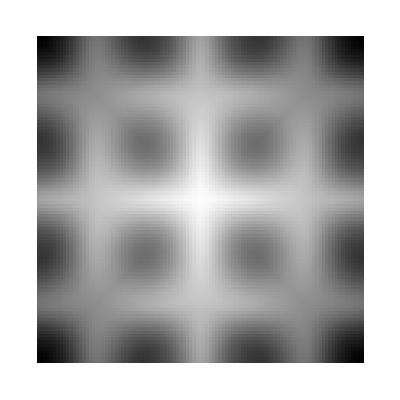

```mathematica
ArrayPlot[values]
```

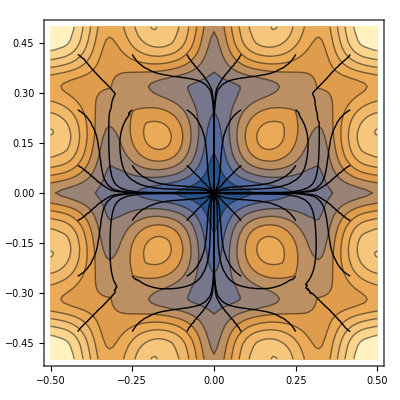

```mathematica
Show[{ListContourPlot[values,Contours->10,DataRange->{{-0.5,0.5},{-0.5,0.5}}],Graphics[Line[geodesics]]}]
```

Convert geodesics to 3D, by adding the z-component:

```mathematica
zcoordinates=Map[{z[Sequence@@#]}&,geodesics,{2}];
```

```mathematica
geodesicsonsurface=Table[Join[geodesics[[i]],zcoordinates[[i]],2],{i,Length[geodesics]}];
```

```mathematica
surface=Map[z[Sequence@@#]&,grid,{2}];
```

```mathematica
Show[{ListPlot3D[surface,DataRange->{{-0.5,0.5},{-0.5,0.5}},Mesh->None],Graphics3D[{Thick,Line[geodesicsonsurface]}]}]
```

-Graphics3D-

### Defining a metric by its eigenvectors and eigenvalues

In this second experiment, inspired by seismic imaging, we consider a metric M with two eigenvalues α^-2 and β^-2. The first one is associated with some normalized eigenvector v, and the second one with the orthogonal direction v^⊥. The metric is defined as

M[x,y]:=α[x,y]^-2 v[x,y]·v[x,y]^T+β[x,y]^-2 v^⊥[x,y]·(v^⊥[x,y])^T.

The inverse tensor field D = M^-1 admits an expression similar to the metric itself:

D[x,y]:=α[x,y]^2 v[x,y]·v[x,y]^T+β[x,y]^2 v^⊥[x,y]·(v^⊥[x,y])^T.

```mathematica
alpha=.8;
v1[x_]:=Normalize@{1,π/2Cos[4π x]};
beta=.2;
v2[x_]:=Normalize@{π/2Cos[4π x],-1};
```

```mathematica
n=101;
gridscale=1/n;
dims={n,n};
dualmetric=Transpose[Table[Transpose[{v1[x],v2[x]}].DiagonalMatrix[{alpha^2,beta^2}].{v1[x],v2[x]},{x,-0.5,0.5,1/(n-1)},{y,-0.5,0.5,1/(n-1)}],{2,1}];
```

```mathematica
dualmetricinputform=Map[{#[[1,1]],#[[1,2]],#[[2,2]]}&,dualmetric,{2}];
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seeds"->seeds,
"gridScale"->gridscale,
"dualMetric"->dualmetricinputform,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"sndOrder"->sndOrder
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.032 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Field exportActiveNeighs defaults to 0

```mathematica
values="values"/.output;
geodesics="geodesics"/.output;
```

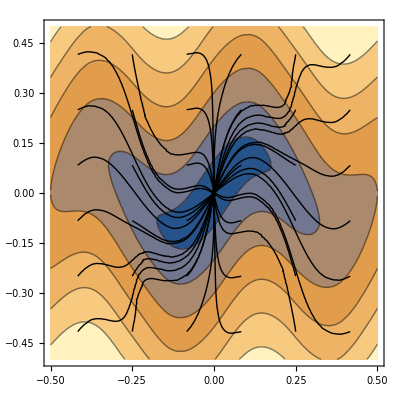

```mathematica
Show[{ListContourPlot[values,Contours->6,DataRange->{{-0.5,0.5},{-0.5,0.5}}],Graphics[Line[geodesics]]}]
```

### Discontinuous and extremely anisotropic Riemannian metric

We illustrate the robustness of the HFM library by considering a hard test case, related with medical image processing, and in particular with tubular structure segmentation. The condition number 100^2 of the metric tensors exceeds what we would typically recommend, namely 10^2 at most. The the discontinuities of the metric fall outside the scope of the mathematical convergence analysis of our numerical method. Nevertheless, the HFM software yields results that are usable and behave as expected qualitatively.
We define a Riemannian metric M:Ω→ S^+ + (ℝ^2) which strongly favors paths remaining close and tangent to a given curve Γ. More precisely, the metric tensor M(p) is defined as the identity matrix, except on a neighborhood of width 0.01 of the spiraling curve parametrized by Γ[t]=t(Cos[ωt],Sin[ωt]), where t∈[0,0.43], and ω=12π. On this extremely thin neighborhood of the curve, the metric tensor has an extremely small eigenvalue 0.01^2 associated with the eigenvector Γ'[t]. The second eigenvalue is 1.

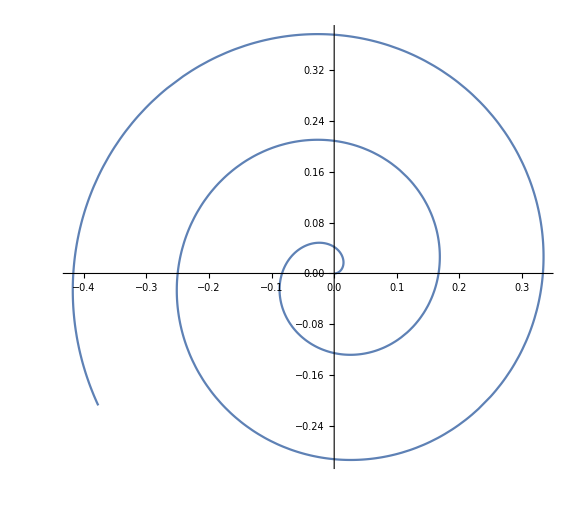

```mathematica
w0=12π;
spiral[t_]:=t{Cos[w0 t],Sin[w0 t]};
ParametricPlot[spiral[t],{t,0,0.43},ImageSize->Large,PlotRange->All]
```

```mathematica
dltt=10.^(-5);
radius=0.01;
delta=0.01;
n=201;
dims={n,n};
```

```mathematica
gridscale=1/n;
```

```mathematica
spiralpoints=Table[spiral[t],{t,0,0.43,dltt}];
```

```mathematica
voxelsize=1./(n+1);
im=Binarize[Image[BinCounts[spiralpoints,{-0.5,0.5,voxelsize},{-0.5,0.5,voxelsize}]],1];
mask=ImageData@Dilation[im,Ceiling[radius/voxelsize]];
```

```mathematica
exportGeodesicFlow=0.;
```

```mathematica
Image@mask
```

-Graphics-

```mathematica
dualmetric=Transpose[Table[If[mask⟦x,y⟧==1,Block[{point={(x-n/2)/n,(y-n/2)/n},tmin,tmax,cw0,sw0,near},
tmin=Floor[Clip[(Norm[point]-radius)/dltt,{1,0.43/dltt+1}]];
tmax=Ceiling[Clip[(Norm[point]+radius)/dltt,{1,0.43/dltt+1}]];
near=Nearest[spiralpoints⟦tmin;;tmax⟧,point,{1,radius}];
If[Length[near]==0,IdentityMatrix[2],
time=Norm[near]; 
cw0=Cos[w0 time];
sw0=Sin[w0 time];
e1=Normalize@{cw0-time w0 sw0,sw0+time w0 cw0};
e2=Normalize@{sw0+time w0 cw0,-cw0+time w0 sw0};
l1=delta^2;
l2=1;
Inverse[Transpose[{e1,e2}].DiagonalMatrix[{l1,l2}].{e1,e2}]
]],IdentityMatrix[2]],{x,1,n},{y,1,n}],{2,1}];//AbsoluteTiming
```

{1.95419,Null}

```mathematica
dualmetricinputform=Map[{#[[1,1]],#[[1,2]],#[[2,2]]}&,dualmetric,{2}];
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seeds"->seeds,
"gridScale"->gridscale,
"dualMetric"->dualmetricinputform,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"sndOrder"->sndOrder
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 0.063 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 4.225
Tip {-0.416667,-0.416667} yields 7 restarts, geodesicVolumeBound increased to 9.28233 .
Tip {-0.416667,-0.25} yields 9 restarts, geodesicVolumeBound increased to 15.6871 .
Tip {-0.416667,-0.0833333} yields 11 restarts, geodesicVolumeBound increased to 26.5112 .
Tip {-0.416667,0.0833333} yields 8 restarts, geodesicVolumeBound increased to 12.067 .
Tip {-0.416667,0.25} yields 11 restarts, geodesicVolumeBound increased to 26.5112 .
Tip {-0.416667,0.416667} yields 11 restarts, geodesicVolumeBound increased to 26.5112 .
Tip {-0.25,0.0833333} yields 6 restarts, geodesicVolumeBound increased to 7.14025 .
Tip {-0.25,0.416667} yields 6 restarts, geodesicVolumeBound increased to 7.14025 .
Tip {-0.0833333,0.416667} yields 6 restarts, geodesicVolumeBound increased to 7.14025 .
Tip {0.0833333,-0.416667} yields 6 restarts, geodesicVolumeBound increased to 7.14025 .
Tip {0.0833333,-0.25} yields 8 restarts, geodesicVolumeBound increased to 12.067 .
Tip {0.0833333,0.416667} yields 6 restarts, geodesicVolumeBound increased to 7.14025 .
Tip {0.25,0.25} yields 7 restarts, geodesicVolumeBound increased to 9.28233 .
Tip {0.25,0.416667} yields 6 restarts, geodesicVolumeBound increased to 7.14025 .
Tip {0.416667,-0.25} yields 7 restarts, geodesicVolumeBound increased to 9.28233 .
Tip {0.416667,-0.0833333} yields 10 restarts, geodesicVolumeBound increased to 20.3933 .
Tip {0.416667,0.25} yields 6 restarts, geodesicVolumeBound increased to 7.14025 .
Tip {0.416667,0.416667} yields 6 restarts, geodesicVolumeBound increased to 7.14025 .
Field exportActiveNeighs defaults to 0

```mathematica
values="values"/.output;
geodesics="geodesics"/.output;
```

```mathematica
ListContourPlot[values,Contours->7,DataRange->{{-0.5,0.5},{-0.5,0.5}}]
```

-Graphics-

```mathematica
Show[{ListContourPlot[values,Contours->6,DataRange->{{-0.5,0.5},{-0.5,0.5}}],Graphics[Line[geodesics]]}]
```

-Graphics-

## Three-dimensional examples

We conclude this notebook with by solving some three dimensional minimal path problems, with respect to anisotropic Riemannian metrics. Two test cases are considered, generalizing the two dimensional ones. More precisely, we illustrate:

the accuracy of our discretization with a test involving a smooth Riemannian metric.
the robustness of our method with a second test case involving a strongly an anisotropic and discontinuous metric.

```mathematica
model="Riemann3";
arrayOrdering="YXZ_RowMajor";
```

#### A smooth Riemannian metric

We generalize to 3D the test case above, based on a metric defined by its eigenvectors and eigenvalues. Our Riemannian metric tensors again have two eigenvalues α^-2 and β^-2. The former is associated with a field of unit vectors, and the latter with the orthogonal plane. For any p = (x,y,z)∈ℝ^3, we let M(p)=(α(p))^-2 v(p)·(v(p))^T+ (β(p))^-2(Id_3-v(p)·(v(p))^T).
As in the 2D case, the dual metric D = M^-1 is obtained by reciprocating the coefficients: D(p)=(α(p))^2 v(p)·(v(p))^T+ (β(p))^2(Id_3-v(p)·(v(p))^T).

```mathematica
n=101;
dims={n,n,n};
gridscale=1./n;
origin={-0.5,-0.5,-0.5};
seeds={{0.,0.,0.}};
```

```mathematica
exportValues=1;
exportGeodesicFlow=0.;
```

```mathematica
sndOrder=1.;
```

```mathematica
tips=Flatten[Table[{i,j,k},{i,-0.5+1/8,0.5-1/8,1/4},{j,-0.5+1/8,0.5-1/8,1/4},{k,-0.5+1/8,0.5-1/8,1/4}],2];
```

```mathematica
alpha=0.2;
beta=0.8;
```

```mathematica
v1[x_,y_,z_]:=Normalize@{Cos[3.0π(x+y)],Sin[3.0π(2x-y)],0.5};
```

```mathematica
dualmetric=Table[ConstantArray[alpha^2 Transpose[{v1[x,y,0]}].{v1[x,y,0]}-beta^2 Transpose[{v1[x,y,0]}].{v1[x,y,0]}+beta^2(IdentityMatrix[3]),n],{x,-0.5,0.5,1/(n-1)},{y,-0.5,0.5,1/(n-1)}];
```

```mathematica
dualmetricinputform=Map[{#[[1,1]],#[[2,1]],#[[2,2]],#[[3,1]],#[[3,2]],#[[3,3]]}&,dualmetric,{3}];
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seeds"->seeds,
"gridScale"->gridscale,
"dualMetric"->dualmetricinputform,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
"arrayOrdering"->arrayOrdering,
"sndOrder"->sndOrder
};
```

```mathematica
output=runHFM["test",params];
"log"/.output
```

Field verbosity defaults to 1
Field showProgress defaults to 0
Fast marching solver completed in 10.459 s.
Field geodesicSolver defaults to Discrete
Field geodesicStep defaults to 0.25
Field geodesicWeightThreshold defaults to 0.0001
Field geodesicVolumeBound defaults to 5.4925
Field exportActiveNeighs defaults to 0

```mathematica
values="values"/.output;
geodesics="geodesics"/.output;
```

```mathematica
Graphics3D[Line[geodesics]]
```

-Graphics3D-

```mathematica
ListContourPlot3D[values,Contours->{.3}]
```

-Graphics3D-

### A discontinuous and strongly anisotropic Riemannian metric

The second 3D example involves discontinuous and strongly anisotropic three dimensional Riemannian metric, which favors paths remaining close and tangent to the curve Γ:[0,3]→ℝ^3 of parametrization Γ[t]:=(Cos[ω t],Sin[ω t],t) ,
where ω=5π/2. More precisely, the metric tensors are equal to the identity matrix, except on a tube of radius 0.02 around the curve Γ, where they have eigenvalues (0.02^2,1,1), the former being associated with the tangent vector Γ'[t].

This test case is inspired by applications to tubular structure segmentation. The condition number 50^2 of these metric tensors, significantly exceeds what we would advise, namely 10^2 at most. In addition, it falls outside the scope of our mathematical convergence analysis, due to its discontinuities. Nevertheless, the obtained numerical results are qualitatively satisfying, illustrating the robustness of our numerical method.

```mathematica
w0=(5/2)π;
delta=0.02;
radius=0.02;
n = 150;
nz=Round[3/2.2n];
dims={n,n,nz};
```

```mathematica
model="Riemann3";
arrayOrdering="YXZ_RowMajor";
```

```mathematica
gridscale=2.2/n;
```

```mathematica
dltt=10.^(-5);
```

```mathematica
spiralpoints=Table[{Cos[w0 t],Sin[w0 t],t},{t,0,3.,dltt}];
```

```mathematica
im=Binarize[Image3D[BinCounts[spiralpoints,{-1.1,1.1,gridscale},{-1.1,1.1,gridscale},{0,3,3/(nz)}]],1];
mask=ImageData@Dilation[im,Ceiling[radius/gridscale]];
```

```mathematica
(*Image of the mask, where the metric is anisotropic*)
Image3D[mask]
```

-Graphics3D-

```mathematica
(*to compute the tangents to the spiral (depending on the z-coordinate)*)
tangent=Transpose[Table[ConstantArray[Normalize[w0{-Sin[w0 t],Cos[w0 t],1./w0}],{n,n}],{t,0,3,3/(nz-1)}],{3,1,2,4}];
```

```mathematica
(*replace tangents with (0,0,0) where the mask is 0*)
tangents=MapThread[#1*#2&,{mask,tangent},2];
```

```mathematica
alpha=.02;
beta=1;
```

```mathematica
(*compute the dual metric*)
dualmetric=Map[If[Max[#]==0.,IdentityMatrix[3],alpha^-2 Transpose[{#}].{#}-beta^-2 Transpose[{#}].{#}+beta^-2(IdentityMatrix[3])]&,tangents,{3}];
```

```mathematica
dualmetricinputform=Map[{#[[1,1]],#[[2,1]],#[[2,2]],#[[3,1]],#[[3,2]],#[[3,3]]}&,dualmetric,{3}];
```

```mathematica
origin={-1.1,-1.1,0.};
seeds={{0.,0.,0.01}};
gridscale=2.2/n;
```

```mathematica
(*to select a single tip on the opposite side to the seed point*)
tips={{0.,0.,2.99}};
```

```mathematica
(*to select a large number of tips on the opposite side to the seed point*)
tips=Flatten[Table[{i,j,2.99},{i,-1.,1.,0.1},{j,-1.,1.,0.1}],1];
```

```mathematica
exportValues=1;
exportGeodesicFlow=0;
```

```mathematica
sndOrder=1.;
```

```mathematica
params = {"model"->model,
"origin"->origin,
"seeds"->seeds,
"gridScale"->gridscale,
"dualMetric"->dualmetricinputform,
"tips"->tips,
"dims"->dims,
"exportValues"->exportValues,
"exportGeodesicFlow"->exportGeodesicFlow,
(*"arrayOrdering"->arrayOrdering,*)
"sndOrder"->sndOrder
};
```

```mathematica
output=runHFM["test",params];
(*"log"/.output*)
```

```mathematica
values="values"/.output;
geodesics="geodesics"/.output;
```

We only save raster images of these experiments in order to reduce the notebook size.

```mathematica
Rasterize[Image3D[Transpose[Chop[ⅇ^(-2.values^2)],{3,2,1}]],RasterSize->600]
```

-Graphics-

```mathematica
Rasterize[Graphics3D[Line[geodesics]],RasterSize->600]
```

-Graphics-